19

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

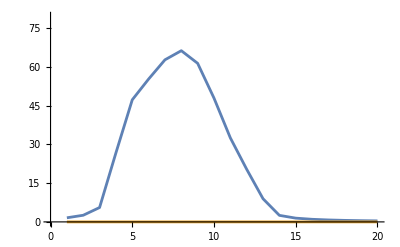

foldedoc.xls

{3.1358,4.93405,9.2375,19.7074,30.6971,37.2411,41.625,43.0897,40.0563,32.7834,24.0288,16.0885,9.21555,4.80873,2.94599,2.05182,1.53368,1.1988,0.966913,0.79846}

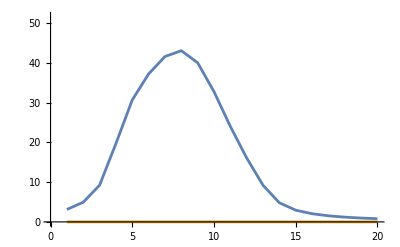

{{{25,-8.5},{125,-8.5},{115,-9},{105,-9.5},{95,-10},{85,-11},{75,-11.5},{65,-11.5},{55,-11},{45,-10.7},{35,-10.5},{25,-8.5}}}

foldedum.xls

-Graphics-

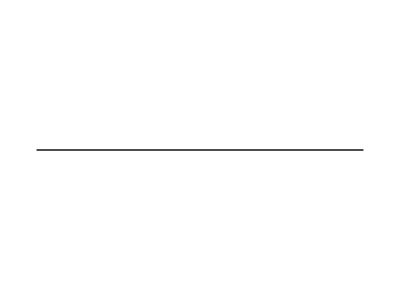

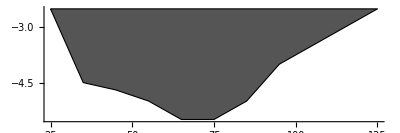

-Graphics-

-Graphics-

{{0,1.8065},{10,2.92316},{20,6.27685},{30,26.553},{40,46.4896},{50,54.6701},{60,61.9264},{70,65.2662},{80,60.4592},{90,47.4065},{100,32.4264},{110,20.4113},{120,9.25458},{130,2.8956},{140,1.66311},{150,1.14815},{160,0.856561},{170,0.669274},{180,0.539851},{190,0.44589}}

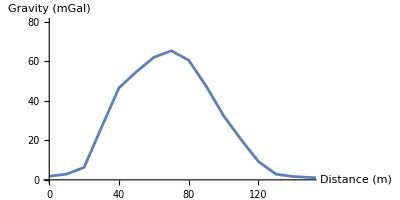

-Graphics-

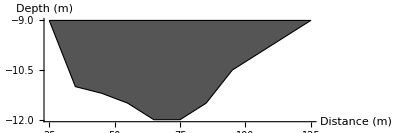

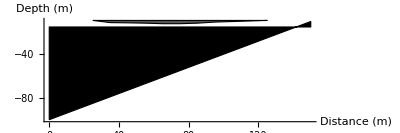

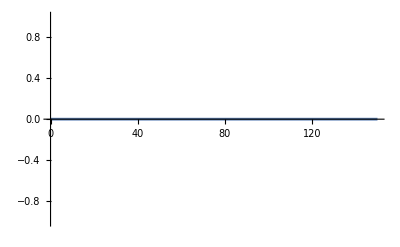

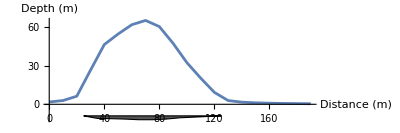

{{0,1.53957},{10,2.58277},{20,5.84642},{30,26.1123},{40,46.1361},{50,54.2485},{60,61.5221},{70,64.8563},{80,60.0618},{90,47.0057},{100,32.0347},{110,20.0439},{120,8.85698},{130,2.48522},{140,1.24308},{150,0.673604},{160,0.315785},{170,0.0177725},{180,-0.281812},{190,-0.856928}}

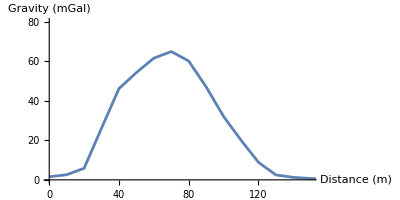

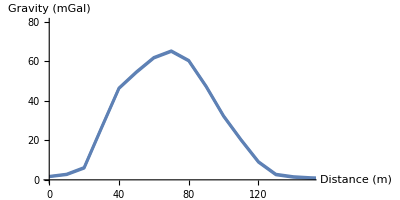

{{0,1.8065,1.53957},{10,2.92316,2.58277},{20,6.27685,5.84642},{30,26.553,26.1123},{40,46.4896,46.1361},{50,54.6701,54.2485},{60,61.9264,61.5221},{70,65.2662,64.8563},{80,60.4592,60.0618},{90,47.4065,47.0057},{100,32.4264,32.0347},{110,20.4113,20.0439},{120,9.25458,8.85698},{130,2.8956,2.48522},{140,1.66311,1.24308},{150,1.14815,0.673604},{160,0.856561,0.315785},{170,0.669274,0.0177725},{180,0.539851,-0.281812},{190,0.44589,-0.856928}}

OutputStream[…]

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Close::stream: {{0,1.8065,1.53957},{10,2.92316,2.58277},{20,6.27685,5.84642},{30,26.553,26.1123},{40,46.4896,46.1361},{50,54.6701,54.2485},{60,61.9264,61.5221},{70,65.2662,64.8563},{80,60.4592,60.0618},{90,47.4065,47.0057},«10»} is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close[{{0,1.8065,1.53957},{10,2.92316,2.58277},{20,6.27685,5.84642},{30,26.553,26.1123},{40,46.4896,46.1361},{50,54.6701,54.2485},{60,61.9264,61.5221},{70,65.2662,64.8563},{80,60.4592,60.0618},{90,47.4065,47.0057},{100,32.4264,32.0347},{110,20.4113,20.0439},{120,9.25458,8.85698},{130,2.8956,2.48522},{140,1.66311,1.24308},{150,1.14815,0.673604},{160,0.856561,0.315785},{170,0.669274,0.0177725},{180,0.539851,-0.281812},{190,0.44589,-0.856928}}]

Plot::pllim: Range specification qgrv is not of the form {x, xmin, xmax}.

Plot[grv,qgrv]

```mathematica
(*Calculations for folded oceanic crust part*)


p=ReadList["C:\\Users\\LENOVO\\Desktop\\Gravity new techniqueee\\oc.txt",Number];
mm=p[[1]](*No.Of points*)
inte=p[[2]];(*Interval*)
zcal=p[[3]];(*depth from the sea*)
nb=p[[4]];(*No.of Bodies*)
nbc=Table[p[[i]],{i,5,4+nb}];(*No.of Body Coordinates*)
rho=Table[p[[i]],{i,5+nb,4+2*nb}];(*Density*)
n=Apply[Plus,nbc];
bc=Table[p[[i]],{i,5+2*nb,4+2*nb+2*n}];(*Body coordinates*)
grvob=Table[p[[i]],{i,5+2*nb+2*n,5+2*nb+2*n+mm}]
rho=Drop[Flatten[Table[Append[Table[rho[[i]],{j,1,nbc[[i]]-1}],0],{i,1,Length[rho]}]],-1];
s=Table[i,{i,0,mm}]*inte;
xb=Table[bc[[2*i-1]],{i,1,n}];
zb=Table[bc[[2*i]],{i,1,n}]+0.0001+zcal;

(*Caculate the grvaity anomaly*)

xb1=Drop[xb,-1];xb2=Rest[xb];
z1=Drop[zb,-1];z2=Rest[zb];
x1=Table[xb[[i]]-s,{i,1,n-1}];
x2=Table[xb2[[i]]-s,{i,1,n-1}];
phi=ArcTan[xb1-xb2,z2-z1];
t1=ArcTan[x1,z1];t2=ArcTan[x2,z2];t12=t1-t2;
r=Sqrt[x2*x2+z2*z2]/Sqrt[x1*x1+z1*z1];
grv=-rho*13.34((z1*Cos[phi]+x1*Sin[phi])*(t12*Cos[phi]-Log[r]*Sin[phi])+z2*t2-z1*t1);
grv=Apply[Plus,grv];

(*Transfer the calculated gravity anomaly values to the output file grav2dres1*)

grv>>>"grav2dres1.txt";
(*Plot the results*)

gravmax=Max[grv];
gravmaxc=gravmax*1.2;
gravmin=Min[grv];
gravminc=gravmin*1.2;
If[gravmin>0,gravmin=0,gravmin=gravminc];
If[gravmax>0,gravmax=gravmaxc,gravmax=0];
gr1=ListPlot[{grv,grvob},Joined->True,PlotRange->{gravmin,gravmax}]
Table[bc[[2*i]]=-bc[[2*i]],{i,1,n}];
bc=Partition[bc,2];
nbcex=Prepend[nbc,0];
ss=0;
ss=Table[ss=ss+nbcex[[i]],{i,1,Length[nbcex]}];
bcptn=Table[Take[bc,{ss[[i]]+1,ss[[i+1]]}],{i,1,Length[nbc]}];
zmax=Max[zb]*1.2;
 Export["foldedoc.xls",grv,"XLS"]

(*Calculations for folded uppermantle part*)

q=ReadList["C:\\Users\\LENOVO\\Desktop\\Gravity new techniqueee\\um.txt",Number];
qmm=q[[1]];(*No.Of points*)
qinte=q[[2]];(*Interval*)
qzcal=q[[3]];(*depth from the sea*)
qnb=q[[4]];(*No.of Bodies*)
qnbc=Table[q[[i]],{i,5,4+qnb}];(*No.of Body Coordinates*)
qrho=Table[q[[i]],{i,5+qnb,4+2*qnb}];(*Density*)
qn=Apply[Plus,qnbc];
qbc=Table[q[[i]],{i,5+2*qnb,4+2*qnb+2*qn}];(*Body coordinates*)
qgrvob=Table[q[[i]],{i,5+2*qnb+2*n,5+2*qnb+2*qn+qmm}];
qrho=Drop[Flatten[Table[Append[Table[qrho[[i]],{j,1,qnbc[[i]]-1}],0],{i,1,Length[qrho]}]],-1];
qs=Table[i,{i,0,qmm}]*qinte;
qxb=Table[qbc[[2*i-1]],{i,1,qn}];
qzb=Table[qbc[[2*i]],{i,1,qn}]+0.0001+qzcal;

(*Caculate the grvaity anomaly*)

qxb1=Drop[qxb,-1];qxb2=Rest[qxb];
qz1=Drop[qzb,-1];qz2=Rest[qzb];
qx1=Table[qxb[[i]]-qs,{i,1,qn-1}];
qx2=Table[qxb2[[i]]-qs,{i,1,qn-1}];
qphi=ArcTan[qxb1-qxb2,qz2-qz1];
qt1=ArcTan[qx1,qz1];qt2=ArcTan[qx2,qz2];qt12=qt1-qt2;
qr=Sqrt[qx2*qx2+qz2*qz2]/Sqrt[qx1*qx1+qz1*qz1];
qgrv=-qrho*13.34((qz1*Cos[qphi]+x1*Sin[qphi])*(qt12*Cos[qphi]-Log[qr]*Sin[qphi])+qz2*qt2-qz1*qt1);
qgrv=Apply[Plus,qgrv]
(*Transfer the calculated gravity anomaly values to the output file grav2dres1*)

grv>>>"qgrav2dres1.txt";
(*Plot the results*)

qgravmax=Max[qgrv];
qgravmaxc=qgravmax*1.2;
qgravmin=Min[qgrv];
qgravminc=qgravmin*1.2;
If[qgravmin>0,qgravmin=0,qgravmin=qgravminc];
If[qgravmax>0,qgravmax=qgravmaxc,qgravmax=0];
qgr1=ListPlot[{qgrv,qgrvob},Joined->True,PlotRange->{qgravmin,qgravmax}]
Table[qbc[[2*i]]=-qbc[[2*i]],{i,1,qn}];
qbc=Partition[qbc,2];
qnbcex=Prepend[qnbc,0];
qss=0;
qss=Table[qss=qss+qnbcex[[i]],{i,1,Length[qnbcex]}];
qbcptn=Table[Take[qbc,{qss[[i]]+1,qss[[i+1]]}],{i,1,Length[qnbc]}]
qzmax=Max[qzb]*1.2;
Export["foldedum.xls",qgrv,"XLS"]
gr2=Graphics[Line[bcptn],Frame->True,PlotRange->{0,-zmax},EdgeForm[{Thickness[.2], Darker[Yellow]}]]
gr3=Graphics[Line[{{0,0},{mm,0}}]]
gr4=Show[gr2,gr3];

(*foldedsediment =Graphics[{EdgeForm[{Black,Dashed}],Darker[Gray],Polygon[bcptn]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
seawater=Graphics[{EdgeForm[{Black,Thin}],Darker[Blue],Polygon[{{0,0},{150,0},{150,-2},{0,-2}}]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
sediment=Graphics[{EdgeForm[{Black,Thin}],Darker[Gray],Polygon[{{0,-2},{150,-2},{150,-4},{0,-4}}]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
oc=Graphics[{EdgeForm[{Black,Thin}],Darker[Yellow],Polygon[{{0,-4},{150,-4},{150,-10},{0,-10}}]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
foldedoc =Graphics[{EdgeForm[{Black,Dashed}],Darker[Yellow],Polygon[qbcptn]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
um=Graphics[{EdgeForm[{Black,Thin}],Darker[Black],Polygon[{{0,-10},{150,-10},{150,-15},{0,-15}}]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
Show[oc,seawater,foldedsediment, sediment,um,foldedoc]*)

foldedsediment =Graphics[{EdgeForm[{Black,Dashed}],Darker[Gray],Polygon[bcptn]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3]
(*seawater=Graphics[{EdgeForm[{Black,Thin}],Darker[Blue],Polygon[{{0,0},{150,0},{150,-2},{0,-2}}]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
sediment=Graphics[{EdgeForm[{Black,Thin}],Darker[Gray],Polygon[{{0,-2},{150,-2},{150,-4},{0,-4}}]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
oc=Graphics[{EdgeForm[{Black,Thin}],Darker[Yellow],Polygon[{{0,-4},{150,-4},{150,-10},{0,-10}}]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
foldedoc =Graphics[{EdgeForm[{Black,Dashed}],Darker[Yellow],Polygon[qbcptn]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
um=Graphics[{EdgeForm[{Black,Thin}],Darker[Black],Polygon[{{0,-10},{150,-10},{150,-15},{0,-15}}]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
Show[oc,seawater,foldedsediment, sediment,um,foldedoc]*)
Show[foldedsediment]
p=Graphics[{EdgeForm[{Black,Thin}],Darker[Black],Polygon[{{0,-100},{150,-10},{150,-15},{0,-15}}]},PlotRange->All,AxesOrigin->{0,0},Axes->True,AspectRatio->1/3];
Show[p];
out=ListPlot[{qgrv,qgrvob},Joined->True,PlotRange->{qgravmin,qgravmax}]
aas=Import["C:\\Users\\LENOVO\\Desktop\\Gravity new techniqueee\\1.csv"]
aaa=ListLinePlot[aas,PlotRange->{{0,150},{0,80}},AxesOrigin->{0,0},Axes->True,AspectRatio->1/2,AxesLabel->{"Distance (m)","Gravity (mGal)"}]
Show[aaa,foldedsediment]
p4=Graphics[{EdgeForm[{Black,Dashed}],Darker[Gray],Polygon[{{25,-9.0},{125,-9.0},{115,-9.5},{105,-10.0},{95,-10.5},{85,-11.5},{75,-12.0},{65,-12.0},{55,-11.5},{45,-11.2},{35,-11.0},{25,-9.0}}]},PlotRange->{{0,150},{0,-12}},AxesOrigin->{0,0},Axes->True,AspectRatio->1/3,AxesLabel->{"Distance (m)","Depth (m)"}]
Show[p4,p]
p5=Plot[0,{x,0,150}]
Show[p4,aaa]
axa1=Import["C:\\Users\\LENOVO\\Desktop\\Gravity new techniqueee\\2.csv"]
axa2=ListLinePlot[axa1,PlotRange->{{0,150},{0,80}},AxesOrigin->{0,0},Axes->True,AspectRatio->1/2,AxesLabel->{"Distance (m)","Gravity (mGal)"}]
Show[aaa,axa2]

axa1=ReadList["C:\\Users\\LENOVO\\Desktop\\Gravity new techniqueee\\2.txt",Number,RecordLists->True]
bbb=OpenWrite["C:\\Users\\LENOVO\\Desktop\\Gravity new techniqueee\\2out.txt"]
Table[Write[bbb,{axa1[[i,1]],axa1[[i,2]],axa1[[i,3]]}],{i,1,Length[axa1]}]
Close[axa1]
Plot[grv,qgrv]
```